{u Cos[v],u Sin[v]}

{u,0,5}

{v,0,2 π}

24

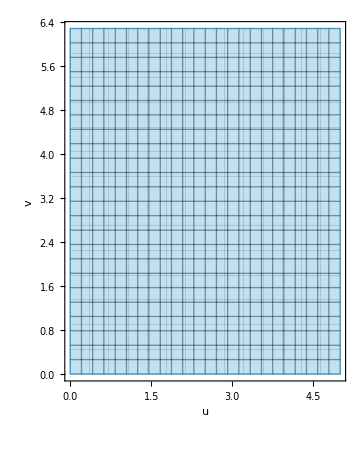
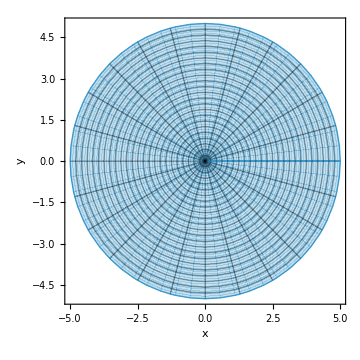
Before | After
-Graphics- | -Graphics-

```mathematica
coords={u Cos[v], u Sin[v]}
bounds1={u,0,5}
bounds2={v,0,2Pi}
meshLines=24
Grid[{{"Before","After"},{
ParametricPlot[{u,v},bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{u,v}],
ParametricPlot[coords,bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{x,y}]
}}]
```

```mathematica
coords={u Cos[v],u Sin[v]}
bounds1={u,0,6}
bounds2={v,0,2Pi}
meshLines=12
Manipulate[
Grid[{{"Before","After"},{
Show[
ParametricPlot[{u,v},bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{u,v}],
ParametricPlot[{u,v},
{u,ustart,ustart+(bounds1[[3]]-bounds1[[2]])/meshLines},
{v,vstart,vstart+(bounds2[[3]]-bounds2[[2]])/meshLines}]
],
Show[
ParametricPlot[coords,bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{x,y}],
ParametricPlot[coords,
{u,ustart,ustart+(bounds1[[3]]-bounds1[[2]])/meshLines},
{v,vstart,vstart+(bounds2[[3]]-bounds2[[2]])/meshLines}]]
}}]
,
{ustart,bounds1[[2]],bounds1[[3]]},
{vstart,bounds2[[2]],bounds2[[3]]}
]
```

{u Cos[v],u Sin[v]}

{u,0,6}

{v,0,2 π}

12

{u Cos[v],u Sin[v]}

{u,0,6}

{v,0,2 π}

12

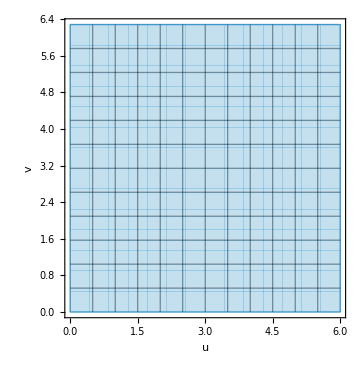
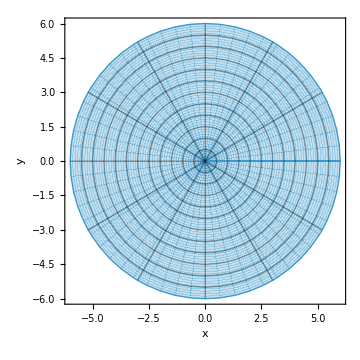
Before | After
-Graphics- | -Graphics-

```mathematica
coords={u Cos[v],u Sin[v]}
bounds1={u,0,6}
bounds2={v,0,2Pi}
meshLines=12
Grid[{{"Before","After"},{
ParametricPlot[{u,v},bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{u,v}],
ParametricPlot[coords,bounds1,bounds2, Mesh->meshLines-1,ImageSize->Medium, AxesLabel->{x,y}]
}}]
```